```mathematica
#kAP=(Scyto/Vcyto)^(2+2*alpha)*10^(-3);
#kPA=10^(-4);
Vcyto=2.5*10^(4);
Scyto=4.4*10^(3);
NA=2.4*10^(5);
NP=9.8*10^(4);
koffA=3.24*10^(-3);
koffP=7.19*10^(-3);
konA=6.29*10^(-3)*Scyto/Vcyto;
konP=7.682*10^(-2)*Scyto/Vcyto;
alpha=2;
beta=2;

Animate[Plot[{

A-(konA*NA)/(koffA+konA+(Scyto/Vcyto)^(2+2*alpha)*10^(kAP)*(konP*NP/(koffP+konP+(Scyto/Vcyto)^(2+2*beta)*10^(kPA)*A^beta))^alpha)==0},{A,0,10^5}],{kAP,-5, -2,Appearance->"Labeled"},{kPA, -5, -2,Appearance->"Labeled"} ,AnimationRunning->False]
```

Set::write: Tag Slot in #kAP is Protected.

Set::write: Tag Slot in #kPA is Protected.

```mathematica
v1=List[];
v2=List[];
For[i=0,i<5000,i++,
k1=RandomReal[{-6,-1}];
k2=RandomReal[{-6,-1}];
n=CountRoots[x-(konA*NA)/(koffA+konA+(Scyto/Vcyto)^(2+2*alpha)*10^(k1)*(konP*NP/(koffP+konP+(Scyto/Vcyto)^(2+2*beta)*10^(k2)*x^beta))^alpha),{x,0,100000}];
If[n>2,AppendTo[v1,k1]];
If[n>2,AppendTo[v2,k2]];

;]
```

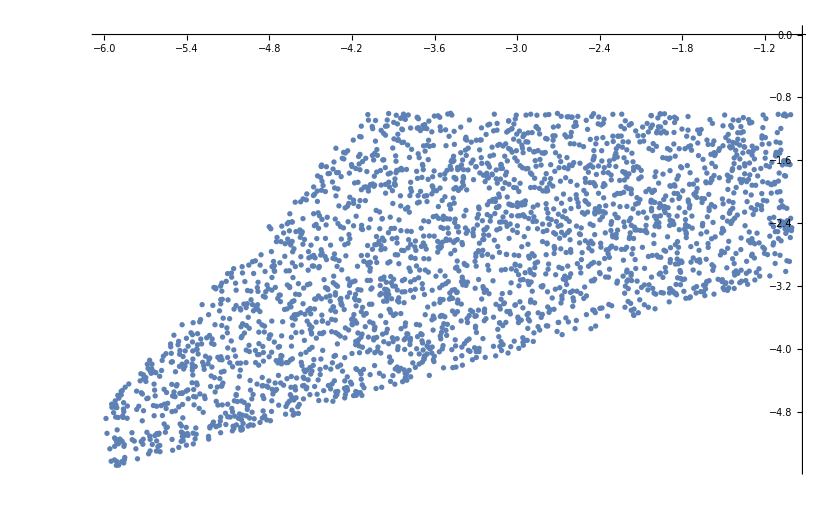

```mathematica
sData=Thread[{v1,v2}];
ListPlot[sData]
```

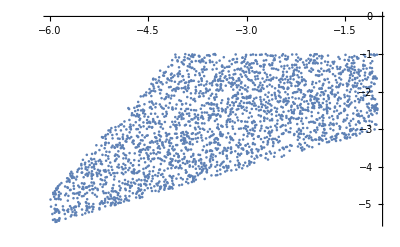

```mathematica
Show[%76,Method->{"AxesInFront"->False,"CoordinatesToolOptions"->{"DisplayFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&)}}]
```

```mathematica
a=CountRoots[x-(konA*NA)/(koffA+konA+(Scyto/Vcyto)^(2+2*alpha)*10^(-3)*(konP*NP/(koffP+konP+(Scyto/Vcyto)^(2+2*beta)*10^(-2)*x^beta))^alpha),{x,0,100000}];
if[a>2,Y=1,Y=2];
Print[Y]
```

2

```mathematica
a
```

3